```mathematica
F[x1_,x2_]=x1^4+x2^4-2 x1^2 -4x1 x2-2 x2^2 ; (* задана функція *)
X={{1.,-1.}}; (*початкове наближення*)
ϵ=10^-3; (*задана точність*)
```

```mathematica
(*значення мінімума, знайдене за допомогою вбудованої функції*)
```

```mathematica
MinF=FindMinimum[F[x1,x2],{{x1,X[[-1,1]]},{x2,X[[-1,2]]}}][[2,1;;2,2]]
```

{1.41421,1.41421}

```mathematica
(*графік тривимірної реалізації*)
Show[Plot3D[F[x,y],{x,-4,4},{y,-4,4}]]
```

-Graphics3D-

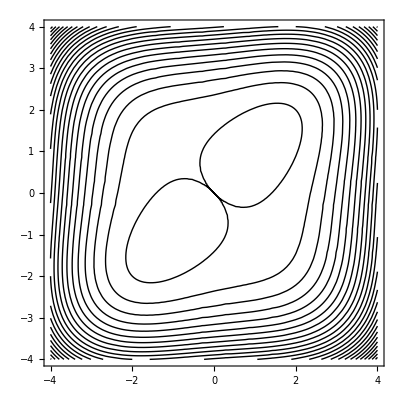

```mathematica
(*двовимірний графік ліній рівня*) 
CP=ContourPlot[F[x,y],{x,-4,4},{y,-4,4},Contours->{Automatic,50},ContourShading->None,AspectRatio->Automatic]
```

```mathematica
(* градієнтний метод з дробленням кроку *)
```

```mathematica
t10=AbsoluteTime[]; (*початок відліку часу*)
X1=X;
α=0.07;  (*крок, підібраний, щоб було якомога менше ітервцій*)
αk=α; 
res1={};
k=1;
While[Norm[Grad[F[x1,x2],{x1,x2}]/.{x1->X1[[-1,1]],x2->X1[[-1,2]]}]>ϵ,{
If[Length[X1]≥1000,Break[]];
AppendTo[X1,X1[[-1]]-αk*Grad[F[x1,x2],{x1,x2}]/.{x1->X1[[-1,1]],x2->X1[[-1,2]]}];
If[F[X1[[-2,1]],X1[[-2,2]]]>F[X1[[-1,1]],X1[[-1,2]]],{
αk=α;
AppendTo[res1,{k++,X1[[-1]],F[X1[[-1,1]],X1[[-1,2]]],αk}];
(* 7 пункт *)
Continue[];
},{
αk/=2;
Delete[X1,-1];
Continue[];
}]
}]
t11=AbsoluteTime[]; 
Grid[Prepend[res1,{"k","x^*","F(x^*)","α_k"}]]
Print["Час роботи методу: ",t1=t11-t10,"\nТочне наближення: ", X1[[-1]],"\nЗначеня функції в отриманому значенні: ", F[X1[[-1,1]],X1[[-1,2]]]]
```

k | x^* | F(x^*) | α_k
1 | {0.72,-0.72} | 0.537477 | 0.07
2 | {0.615491,-0.615491} | 0.287022 | 0.07
3 | {0.550204,-0.550204} | 0.183284 | 0.07
4 | {0.503567,-0.503567} | 0.128606 | 0.07
5 | {0.467813,-0.467813} | 0.0957896 | 0.07
6 | {0.439146,-0.439146} | 0.0743819 | 0.07
7 | {0.415433,-0.415433} | 0.0595711 | 0.07
8 | {0.395358,-0.395358} | 0.0488644 | 0.07
9 | {0.378055,-0.378055} | 0.0408553 | 0.07
10 | {0.362925,-0.362925} | 0.0346976 | 0.07
11 | {0.349541,-0.349541} | 0.0298552 | 0.07
12 | {0.337583,-0.337583} | 0.0259747 | 0.07
13 | {0.326811,-0.326811} | 0.0228147 | 0.07
14 | {0.317037,-0.317037} | 0.0202056 | 0.07
15 | {0.308115,-0.308115} | 0.0180252 | 0.07
16 | {0.299925,-0.299925} | 0.0161837 | 0.07
17 | {0.29237,-0.29237} | 0.0146138 | 0.07
18 | {0.285373,-0.285373} | 0.0132641 | 0.07
19 | {0.278865,-0.278865} | 0.0120951 | 0.07
20 | {0.272793,-0.272793} | 0.0110755 | 0.07
21 | {0.267109,-0.267109} | 0.0101809 | 0.07
22 | {0.261773,-0.261773} | 0.00939138 | 0.07
23 | {0.25675,-0.25675} | 0.00869109 | 0.07
24 | {0.252011,-0.252011} | 0.00806696 | 0.07
25 | {0.24753,-0.24753} | 0.00750828 | 0.07
26 | {0.243283,-0.243283} | 0.00700614 | 0.07
27 | {0.239252,-0.239252} | 0.00655313 | 0.07
28 | {0.235417,-0.235417} | 0.006143 | 0.07
29 | {0.231764,-0.231764} | 0.00577048 | 0.07
30 | {0.228278,-0.228278} | 0.00543108 | 0.07
31 | {0.224947,-0.224947} | 0.00512097 | 0.07
32 | {0.22176,-0.22176} | 0.00483686 | 0.07
33 | {0.218706,-0.218706} | 0.0045759 | 0.07
34 | {0.215777,-0.215777} | 0.00433564 | 0.07
35 | {0.212964,-0.212964} | 0.00411393 | 0.07
36 | {0.21026,-0.21026} | 0.00390891 | 0.07
37 | {0.207657,-0.207657} | 0.00371892 | 0.07
38 | {0.20515,-0.20515} | 0.00354254 | 0.07
39 | {0.202732,-0.202732} | 0.00337848 | 0.07
40 | {0.200399,-0.200399} | 0.00322563 | 0.07
41 | {0.198146,-0.198146} | 0.00308297 | 0.07
42 | {0.195968,-0.195968} | 0.00294962 | 0.07
43 | {0.19386,-0.19386} | 0.00282479 | 0.07
44 | {0.19182,-0.19182} | 0.00270775 | 0.07
45 | {0.189844,-0.189844} | 0.00259788 | 0.07
46 | {0.187928,-0.187928} | 0.00249459 | 0.07
47 | {0.18607,-0.18607} | 0.00239737 | 0.07
48 | {0.184266,-0.184266} | 0.00230575 | 0.07
49 | {0.182514,-0.182514} | 0.00221931 | 0.07
50 | {0.180812,-0.180812} | 0.00213766 | 0.07
51 | {0.179157,-0.179157} | 0.00206045 | 0.07
52 | {0.177547,-0.177547} | 0.00198738 | 0.07
53 | {0.17598,-0.17598} | 0.00191813 | 0.07
54 | {0.174454,-0.174454} | 0.00185246 | 0.07
55 | {0.172967,-0.172967} | 0.00179012 | 0.07
56 | {0.171518,-0.171518} | 0.00173089 | 0.07
57 | {0.170105,-0.170105} | 0.00167456 | 0.07
58 | {0.168727,-0.168727} | 0.00162095 | 0.07
59 | {0.167382,-0.167382} | 0.00156988 | 0.07
60 | {0.16607,-0.166068} | 0.00152119 | 0.07
61 | {0.164788,-0.164786} | 0.00147475 | 0.07
62 | {0.163535,-0.163532} | 0.0014304 | 0.07
63 | {0.162311,-0.162307} | 0.00138804 | 0.07
64 | {0.161115,-0.161109} | 0.00134754 | 0.07
65 | {0.159946,-0.159936} | 0.00130878 | 0.07
66 | {0.158803,-0.158788} | 0.00127169 | 0.07
67 | {0.157686,-0.157662} | 0.00123615 | 0.07
68 | {0.156595,-0.156558} | 0.00120209 | 0.07
69 | {0.15553,-0.155474} | 0.00116941 | 0.07
70 | {0.154492,-0.154406} | 0.00113806 | 0.07
71 | {0.153484,-0.153351} | 0.00110793 | 0.07
72 | {0.152509,-0.152304} | 0.00107897 | 0.07
73 | {0.151573,-0.151257} | 0.00105106 | 0.07
74 | {0.150686,-0.1502} | 0.00102406 | 0.07
75 | {0.149864,-0.149115} | 0.000997704 | 0.07
76 | {0.149132,-0.147977} | 0.000971445 | 0.07
77 | {0.148526,-0.146746} | 0.000944041 | 0.07
78 | {0.148107,-0.145363} | 0.000912608 | 0.07
79 | {0.147966,-0.143735} | 0.000870353 | 0.07
80 | {0.148244,-0.141718} | 0.00080116 | 0.07
81 | {0.149159,-0.139094} | 0.000666716 | 0.07
82 | {0.151047,-0.135523} | 0.000375826 | 0.07
83 | {0.154429,-0.130479} | -0.000288678 | 0.07
84 | {0.160104,-0.123151} | -0.00184408 | 0.07
85 | {0.169302,-0.112281} | -0.00552244 | 0.07
86 | {0.18391,-0.0959182} | -0.0142564 | 0.07
87 | {0.206806,-0.0710334} | -0.0350135 | 0.07
88 | {0.242345,-0.0329169} | -0.0842699 | 0.07
89 | {0.297,0.025733} | -0.200532 | 0.07
90 | {0.38003,0.116093} | -0.471237 | 0.07
91 | {0.503576,0.25457} | -1.08106 | 0.07
92 | {0.680101,0.462231} | -2.35026 | 0.07
93 | {0.911874,0.754432} | -4.53778 | 0.07
94 | {1.16613,1.10077} | -6.96024 | 0.07
95 | {1.35685,1.36204} | -7.95369 | 0.07
96 | {1.4187,1.41583} | -7.9998 | 0.07
97 | {1.41285,1.41482} | -7.99997 | 0.07
98 | {1.41493,1.41359} | -7.99999 | 0.07
99 | {1.41375,1.41466} | -8. | 0.07
100 | {1.41452,1.4139} | -8. | 0.07
101 | {1.414,1.41442} | -8. | 0.07
102 | {1.41436,1.41407} | -8. | 0.07
103 | {1.41412,1.41431} | -8. | 0.07
104 | {1.41428,1.41415} | -8. | 0.07
105 | {1.41417,1.41426} | -8. | 0.07
106 | {1.41424,1.41418} | -8. | 0.07
107 | {1.41419,1.41423} | -8. | 0.07

Час роботи методу: 0.024588
Точне наближення: {1.41419,1.41423}
Значеня функції в отриманому значенні: -8.

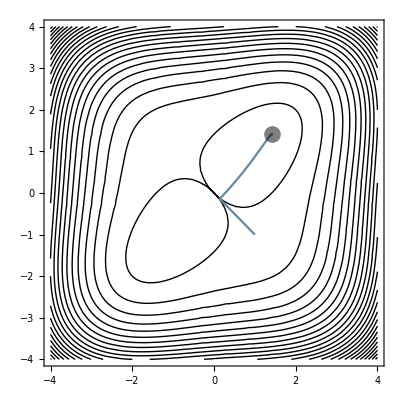

```mathematica
(*траєкторія пошука точки мінімума*)
Show[CP,ListLinePlot[X1,ColorFunction->"Rainbow",PlotRange->All],Graphics[{Opacity[0.5],Black,PointSize[0.03],Point[{MinF[[1]],MinF[[2]]}]}]]
```